```mathematica
Clear["@"];
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear will be suppressed during this calculation.

```mathematica
<<Data`;
<<BISfit`;
```

```mathematica
?ColeP
```

get the resistances(r0,r∞,α)

```mathematica
(* Cole plot and fit compare *)
```

```mathematica
data0=mData[1];
ff=Freq32[];
Dimensions[data0]
pr=data0[[1,All,{5,6}]];
{m,n,r}=BISffit[pr]
```

{1,32,16}

{61.0554,-11.4362,24.9861}

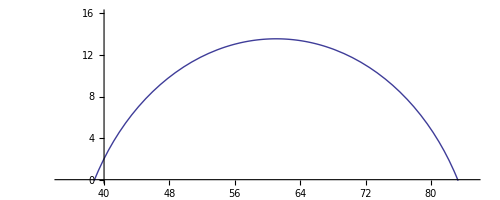

```mathematica
(*fitted one*)
p1=ParametricPlot[{r Cos[th]+m,r Sin[th]+n},{th,π/2-1.1,π/2+1.1},PlotRange->{{35,85},{0,16}}]
```

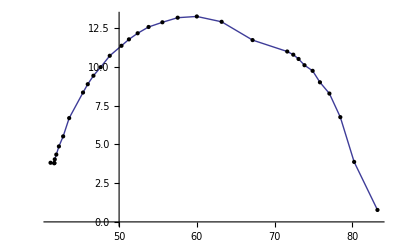

```mathematica
X=Map[ Function[x,x[[1]]Cos[-x[[2]]π/(180)]],pr];
Y=Map[ Function[x,x[[1]]Sin[-x[[2]]π/(180)]],pr];
Z=Table[{X[[i]],Y[[i]]},{i,Length[X]}];
p2=ListPlot[Z,Joined->True,Mesh->Full,MeshStyle->PointSize[Medium]];
```

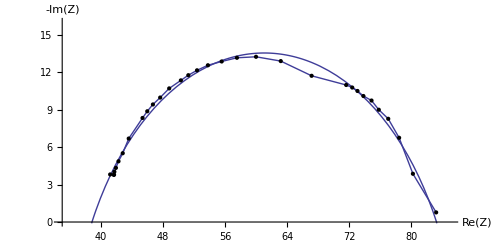

```mathematica
Show[p1,p2,AxesLabel->{"Re(Z)","-Im(Z)"},AxesOrigin->{35,0},AspectRatio->0.5]
```

```mathematica
(* R and X to freq*)
```

```mathematica
RR=Transpose[{ff,X}];
XX=Transpose[{ff,Y}];
```

```mathematica
ff
```

{1000,2000,3000,4000,5000,6000,7000,8000,9000,10000,20000,30000,40000,50000,60000,70000,80000,90000,100000,120000,140000,160000,180000,200000,300000,400000,500000,600000,700000,800000,900000,1000000}

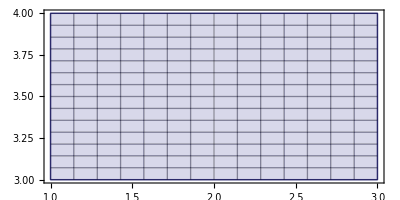

```mathematica
ParametricPlot[{u,v},{u,1,3},{v,3,4},Mesh->Full]
```

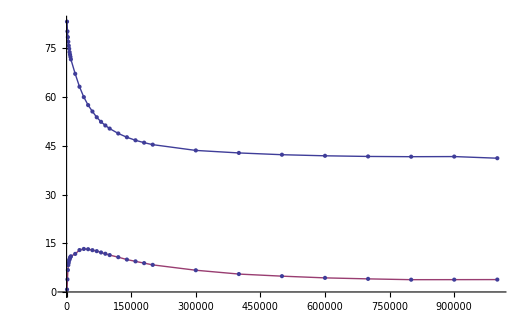

```mathematica
ListPlot[{RR,XX},Joined->True,Mesh->Full]
```

```mathematica
(*log freq plot*)
(*lff=N[Log[10,ff]];
lRR=Transpose[{lff,X}];
lXX=Transpose[{lff,Y}];*)
```

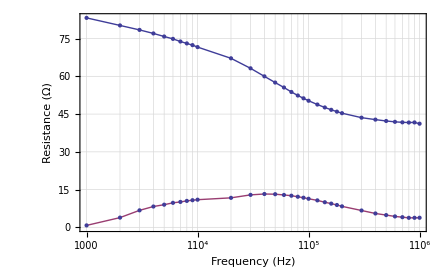

```mathematica
ListLogLinearPlot[{RR,XX},Joined->True,Mesh->Full,GridLines->Automatic,Frame->True,FrameLabel->{"Frequency (Hz)","Resistance (Ω)"}]
```

```mathematica
(* new x r data*)
```

```mathematica
data2=nxrData[2];
ff=Freq23[];
```

```mathematica
Dimensions[data2]
```

```mathematica
pr=data2[[1,1,1]];
```

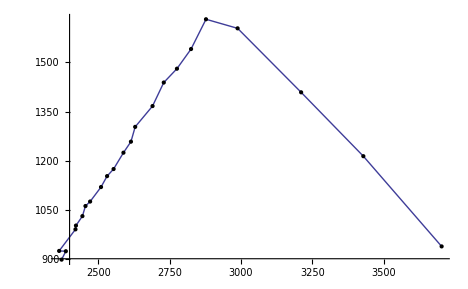

```mathematica
pp1=ListPlot[pr,Joined->True,Mesh->Full,MeshStyle->PointSize[Medium]]
```

```mathematica
xx=pr[[All,1]];
yy=pr[[All,2]];
```

```mathematica
RR=Transpose[{ff,xx}];
XX=Transpose[{ff,yy}];
```

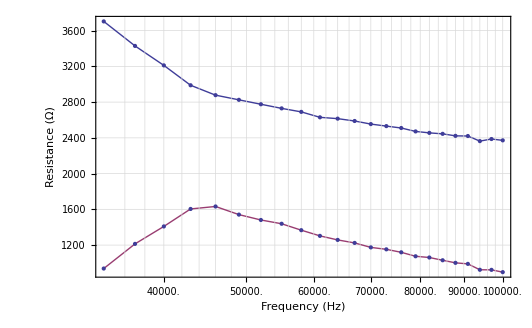

```mathematica
ListLogLinearPlot[{RR,XX},Joined->True,Mesh->Full,GridLines->Automatic,Frame->True,FrameLabel->{"Frequency (Hz)","Resistance (Ω)"}]
```

```mathematica
(*Bode chart,*)
```

```mathematica
z=Table[√(yy[[i]]^2+xx[[i]]^2),{i,Length[yy]}];
ang=Table[ArcTan[xx[[i]],yy[[i]]]/Degree,{i,Length[yy]}]
```

{14.21,19.49,23.69,28.23,29.56,28.61,28.08,27.79,26.93,26.36,25.69,25.31,24.69,24.48,24.03,23.5,23.37,22.85,22.46,22.24,21.35,21.14,20.72}

```mathematica
ZZ=Transpose[{ff,z}];
AA=Transpose[{ff,ang}];
```

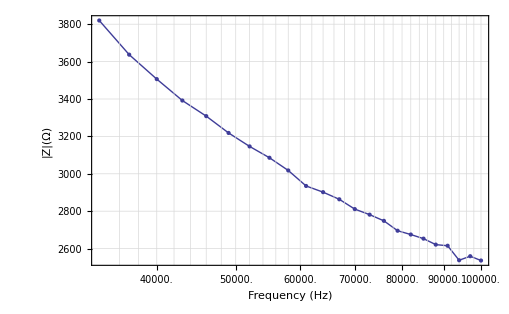

```mathematica
ListLogLinearPlot[{ZZ},Joined->True,Mesh->Full,GridLines->Automatic,Frame->True,FrameLabel->{"Frequency (Hz)","|Z|(Ω)"}]
```

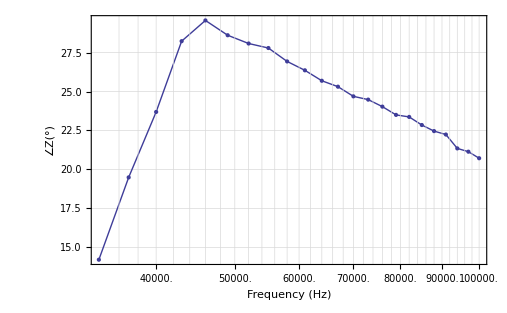

```mathematica
ListLogLinearPlot[{AA},Joined->True,Mesh->Full,GridLines->Automatic,Frame->True,FrameLabel->{"Frequency (Hz)","∠Z(°)"}]
```